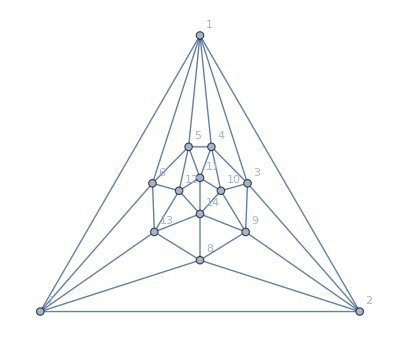

```mathematica
pl1=Graph[plantri[[2]],VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

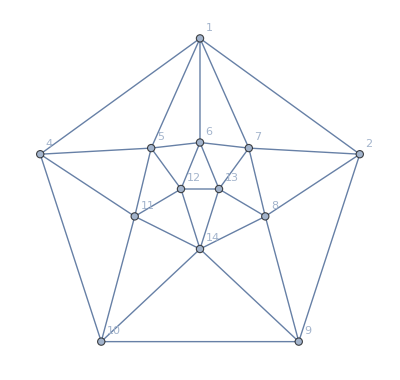

```mathematica
pl2=VertexDelete[pl1,3]
```

```mathematica
ffpl2=FindFullFormula[pl2];
```

```mathematica
HighlightSymbol[s_]:=Row[Map[If[#=="x",Style[#,Red],If[MemberQ[{"1","2","9","a","4"},#],Style[#,Blue],#]]&,StringPartition[SymbolName[s],1]]]
```

```mathematica
HighlightSymbol[v1ex25adx479cx68b]
```

v1ex25adx479cx68b

```mathematica
NotGood[s_]:=SetsToSymbol2[Sort[Map[Sort,SymbolToSets[ Symbol[StringJoin[Select[StringPartition[SymbolName[s],1],!MemberQ[{"1","2","9","a","4"},#]&]]]]],First[#1]<First[#2]&]]
```

```mathematica
Good[s_]:=SetsToSymbol2[Select[Sort[Map[Sort,SymbolToSets[ Symbol [StringJoin[Select[StringPartition[SymbolName[s],1],MemberQ[{"v","x","1","2","9","a","4"},#]&]]]]],First[#1]<First[#2]&],#≠{}&]]
```

```mathematica
Cases
```

```mathematica
pl2gen=TableForm[
Map[Framed[TableForm[#]]&,
GatherBy[
Map[{NotGood[#],With[{g=Good[#]},TableForm[{StringCount[SymbolName[g],"x"],g}, TableDirections->Row]],HighlightSymbol[#]}&,Select[ffpl2,StringCount[SymbolName[#],"x"]==3&]]//Sort,
First]],TableDepth->1]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

v57ex68xbdxc | 2 | v19x24xa | v19bdx24cx57ex68a
v57ex68xbdxc | 2 | v19x2ax4 | v19bdx2acx468x57e
v57ex6bx8cxd | 2 | v1ax24x9 | v18acx24dx57ex69b
v57ex6bx8cxd | 2 | v1ax2x49 | v18acx26bx49dx57e
v57ex6x8cxbd | 2 | v19x24xa | v19bdx246x57ex8ac
v57ex6x8cxbd | 2 | v19x2ax4 | v19bdx26ax48cx57e
v57ex6x8cxbd | 2 | v1ax24x9 | v18acx246x57ex9bd
v57ex6x8cxbd | 2 | v1ax2x49 | v18acx2bdx469x57e
v57x6ex8cxbd | 2 | v19x24xa | v19bdx246ex57ax8c
v57x6ex8cxbd | 2 | v19x24xa | v19bdx246ex57x8ac
v57x6ex8cxbd | 2 | v1ax24x9 | v18acx246ex579xbd
v57x6ex8cxbd | 2 | v1ax24x9 | v18acx246ex57x9bd
v57x6ex8cxbd | 3 | v19x2x4xa | v19bdx26ex48cx57a
v57x6ex8cxbd | 3 | v1ax2x4x9 | v18acx2bdx46ex579
v57x6ex8cxbd | 3 | v1x24x9xa | v18cx246ex57ax9bd
v57x6ex8cxbd | 3 | v1x24x9xa | v1bdx246ex579x8ac
v58x6ex7cxbd | 2 | v19x24xa | v19bdx246ex58ax7c
v58x6ex7cxbd | 2 | v19x24xa | v19bdx246ex58x7ac
v58x6ex7cxbd | 3 | v19x2x4xa | v19bdx26ex47cx58a
v58x6ex7cxbd | 3 | v1x24x9xa | v1bdx246ex58ax79c
v58x6ex7cxbd | 3 | v1x2x49xa | v1bdx26ex479cx58a
v5dx68bx7cxe | 2 | v1x2ax49 | v1ex25adx479cx68b
v5dx68bx7exc | 2 | v19x2ax4 | v19cx25adx47ex68b
v5dx6bx7ex8c | 3 | v1ax2x4x9 | v18acx25dx47ex69b
v5dx6bx7ex8c | 3 | v1ax2x4x9 | v18acx26bx47ex59d
v5dx6bx7ex8c | 3 | v1x2ax4x9 | v18cx25adx47ex69b
v5dx6ex7bx8c | 2 | v1ax24x9 | v18acx246ex5dx79b
v5dx6ex7bx8c | 2 | v1ax24x9 | v18acx246ex59dx7b
v5dx6ex7bx8c | 3 | v1ax2x4x9 | v18acx25dx46ex79b
v5dx6ex7bx8c | 3 | v1x24x9xa | v18cx246ex5adx79b
v5dx6ex7bx8c | 3 | v1x2ax4x9 | v18cx25adx46ex79b
v5dx6ex7cx8b | 2 | v1x2ax49 | v18bx25adx479cx6e
v5dx6ex7cx8b | 3 | v1x24x9xa | v18bx246ex59dx7ac
v5dx6ex7cx8b | 3 | v1x24x9xa | v18bx246ex5adx79c
v5dx6ex7cx8b | 3 | v1x2ax4x9 | v18bx25adx46ex79c
v5dx6ex7cx8b | 3 | v1x2x49xa | v18bx26ex479cx5ad
v5ex68bx7cxd | 2 | v1ax2x49 | v1adx25ex479cx68b
v5ex68x7cxbd | 3 | v19x2x4xa | v19bdx25ex468x7ac
v5ex68x7cxbd | 3 | v19x2x4xa | v19bdx25ex47cx68a
v5ex68x7cxbd | 3 | v1x2x49xa | v1bdx25ex479cx68a

```mathematica
GatherBy[
Map[{NotGood[#],Good[#],HighlightSymbol[#]}&,Select[ffpl2,StringCount[SymbolName[#],"x"]==3&]]//Sort,
First]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{{{v57ex68xbdxc,v19x24xxa,v19bdx24cx57ex68a},{v57ex68xbdxc,v19x2ax4,v19bdx2acx468x57e}},{{v57ex6bx8cxd,v1ax24xx9,v18acx24dx57ex69b},{v57ex6bx8cxd,v1ax2x49,v18acx26bx49dx57e}},{{v57ex6x8cxbd,v19x24xxa,v19bdx246x57ex8ac},{v57ex6x8cxbd,v19x2ax4,v19bdx26ax48cx57e},{v57ex6x8cxbd,v1ax24xx9,v18acx246x57ex9bd},{v57ex6x8cxbd,v1ax2x49,v18acx2bdx469x57e}},{{v57x6ex8cxbd,v19x24xa,v19bdx246ex57ax8c},{v57x6ex8cxbd,v19x24xxa,v19bdx246ex57x8ac},{v57x6ex8cxbd,v19x2x4xa,v19bdx26ex48cx57a},{v57x6ex8cxbd,v1ax24x9,v18acx246ex579xbd},{v57x6ex8cxbd,v1ax24xx9,v18acx246ex57x9bd},{v57x6ex8cxbd,v1ax2x4x9,v18acx2bdx46ex579},{v57x6ex8cxbd,v1x24x9xa,v18cx246ex57ax9bd},{v57x6ex8cxbd,v1x24x9xa,v1bdx246ex579x8ac}},{{v58x6ex7cxbd,v19x24xa,v19bdx246ex58ax7c},{v58x6ex7cxbd,v19x24xxa,v19bdx246ex58x7ac},{v58x6ex7cxbd,v19x2x4xa,v19bdx26ex47cx58a},{v58x6ex7cxbd,v1x24x9xa,v1bdx246ex58ax79c},{v58x6ex7cxbd,v1x2x49xa,v1bdx26ex479cx58a}},{{v5dx68bx7cxe,v1x2ax49,v1ex25adx479cx68b}},{{v5dx68bx7exc,v19x2ax4,v19cx25adx47ex68b}},{{v5dx6bx7ex8c,v1ax2x4x9,v18acx25dx47ex69b},{v5dx6bx7ex8c,v1ax2x4x9,v18acx26bx47ex59d},{v5dx6bx7ex8c,v1x2ax4x9,v18cx25adx47ex69b}},{{v5dx6ex7bx8c,v1ax24x9,v18acx246ex59dx7b},{v5dx6ex7bx8c,v1ax24xx9,v18acx246ex5dx79b},{v5dx6ex7bx8c,v1ax2x4x9,v18acx25dx46ex79b},{v5dx6ex7bx8c,v1x24x9xa,v18cx246ex5adx79b},{v5dx6ex7bx8c,v1x2ax4x9,v18cx25adx46ex79b}},{{v5dx6ex7cx8b,v1x24x9xa,v18bx246ex59dx7ac},{v5dx6ex7cx8b,v1x24x9xa,v18bx246ex5adx79c},{v5dx6ex7cx8b,v1x2ax49,v18bx25adx479cx6e},{v5dx6ex7cx8b,v1x2ax4x9,v18bx25adx46ex79c},{v5dx6ex7cx8b,v1x2x49xa,v18bx26ex479cx5ad}},{{v5ex68bx7cxd,v1ax2x49,v1adx25ex479cx68b}},{{v5ex68x7cxbd,v19x2x4xa,v19bdx25ex468x7ac},{v5ex68x7cxbd,v19x2x4xa,v19bdx25ex47cx68a},{v5ex68x7cxbd,v1x2x49xa,v1bdx25ex479cx68a}}}

```mathematica
TableForm[
Map[Framed[TableForm[#]]&,
GatherBy[
Map[{With[{g=Good[#]},TableForm[{StringCount[SymbolName[g],"x"],g}, TableDirections->Row]],NotGood[#],HighlightSymbol[#]}&,Select[ffpl2,StringCount[SymbolName[#],"x"]==3&]]//Sort,
First]],TableDepth->1]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

2 | v19x24xa | v57ex68xbdxc | v19bdx24cx57ex68a
2 | v19x24xa | v57ex6x8cxbd | v19bdx246x57ex8ac
2 | v19x24xa | v57x6ex8cxbd | v19bdx246ex57ax8c
2 | v19x24xa | v57x6ex8cxbd | v19bdx246ex57x8ac
2 | v19x24xa | v58x6ex7cxbd | v19bdx246ex58ax7c
2 | v19x24xa | v58x6ex7cxbd | v19bdx246ex58x7ac
2 | v19x2ax4 | v57ex68xbdxc | v19bdx2acx468x57e
2 | v19x2ax4 | v57ex6x8cxbd | v19bdx26ax48cx57e
2 | v19x2ax4 | v5dx68bx7exc | v19cx25adx47ex68b
2 | v1ax24x9 | v57ex6bx8cxd | v18acx24dx57ex69b
2 | v1ax24x9 | v57ex6x8cxbd | v18acx246x57ex9bd
2 | v1ax24x9 | v57x6ex8cxbd | v18acx246ex579xbd
2 | v1ax24x9 | v57x6ex8cxbd | v18acx246ex57x9bd
2 | v1ax24x9 | v5dx6ex7bx8c | v18acx246ex5dx79b
2 | v1ax24x9 | v5dx6ex7bx8c | v18acx246ex59dx7b
2 | v1ax2x49 | v57ex6bx8cxd | v18acx26bx49dx57e
2 | v1ax2x49 | v57ex6x8cxbd | v18acx2bdx469x57e
2 | v1ax2x49 | v5ex68bx7cxd | v1adx25ex479cx68b
2 | v1x2ax49 | v5dx68bx7cxe | v1ex25adx479cx68b
2 | v1x2ax49 | v5dx6ex7cx8b | v18bx25adx479cx6e
3 | v19x2x4xa | v57x6ex8cxbd | v19bdx26ex48cx57a
3 | v19x2x4xa | v58x6ex7cxbd | v19bdx26ex47cx58a
3 | v19x2x4xa | v5ex68x7cxbd | v19bdx25ex468x7ac
3 | v19x2x4xa | v5ex68x7cxbd | v19bdx25ex47cx68a
3 | v1ax2x4x9 | v57x6ex8cxbd | v18acx2bdx46ex579
3 | v1ax2x4x9 | v5dx6bx7ex8c | v18acx25dx47ex69b
3 | v1ax2x4x9 | v5dx6bx7ex8c | v18acx26bx47ex59d
3 | v1ax2x4x9 | v5dx6ex7bx8c | v18acx25dx46ex79b
3 | v1x24x9xa | v57x6ex8cxbd | v18cx246ex57ax9bd
3 | v1x24x9xa | v57x6ex8cxbd | v1bdx246ex579x8ac
3 | v1x24x9xa | v58x6ex7cxbd | v1bdx246ex58ax79c
3 | v1x24x9xa | v5dx6ex7bx8c | v18cx246ex5adx79b
3 | v1x24x9xa | v5dx6ex7cx8b | v18bx246ex59dx7ac
3 | v1x24x9xa | v5dx6ex7cx8b | v18bx246ex5adx79c
3 | v1x2ax4x9 | v5dx6bx7ex8c | v18cx25adx47ex69b
3 | v1x2ax4x9 | v5dx6ex7bx8c | v18cx25adx46ex79b
3 | v1x2ax4x9 | v5dx6ex7cx8b | v18bx25adx46ex79c
3 | v1x2x49xa | v58x6ex7cxbd | v1bdx26ex479cx58a
3 | v1x2x49xa | v5dx6ex7cx8b | v18bx26ex479cx5ad
3 | v1x2x49xa | v5ex68x7cxbd | v1bdx25ex479cx68a